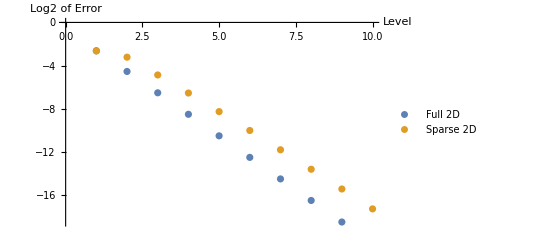

```mathematica
ListPlot[{full2DError,sparse2DError⟦;;10⟧}//Log2,PlotLegends->{"Full 2D","Sparse 2D"},AxesLabel->{"Level","Log2 of Error"}]
```

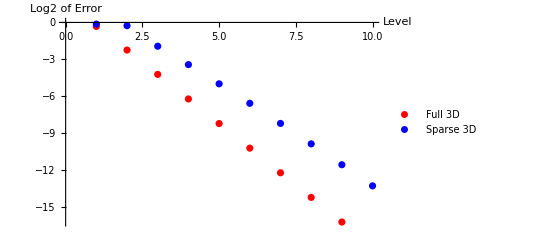

```mathematica
ListPlot[{full3DError,sparse3DError⟦;;10⟧}//Log2,PlotLegends->{"Full 3D","Sparse 3D"},AxesLabel->{"Level","Log2 of Error"},PlotStyle->{Red,Blue}]
```

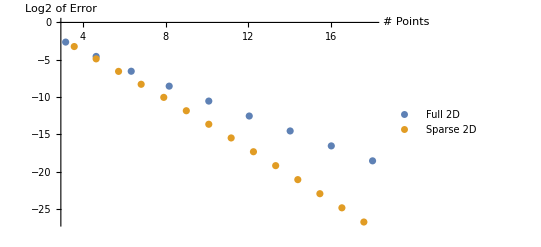

```mathematica
ListPlot[{Table[{hierLengths2D[[n]],full2DError[[n]]},{n,1,9}],Table[{sparseLengths2D[[n]],sparse2DError[[n]]},{n,2,15}]}//Log2,PlotLegends->{"Full 2D","Sparse 2D"},AxesLabel->{"# Points","Log2 of Error"}]
```

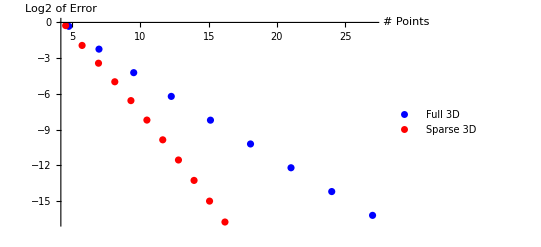

```mathematica
ListPlot[{Table[{hierLengths3D[[n]],full3DError[[n]]},{n,1,9}],Table[{sparseLengths3D[[n]],sparse3DError[[n]]},{n,2,12}]}//Log2,PlotLegends->{"Full 3D","Sparse 3D"},AxesLabel->{"# Points","Log2 of Error"},PlotStyle->{Blue,Red}]
```

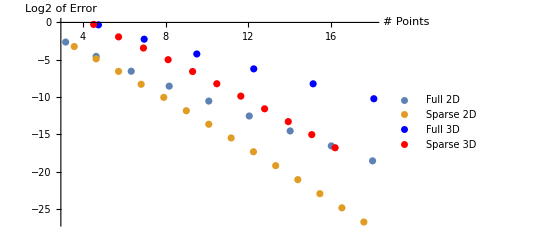

```mathematica
Show[Out[738],Out[750]]
```

```mathematica
D[Log[p]^3/p^2,p] p/(Log[p]^3/p^2)
```

(p^3 ((3 Log[p]^2)/p^3-(2 Log[p]^3)/p^3))/Log[p]^3

```mathematica
D[Log[p]^6/p^2,p] p/(Log[p]^6/p^2)
```

(p^3 ((6 Log[p]^5)/p^3-(2 Log[p]^6)/p^3))/Log[p]^6

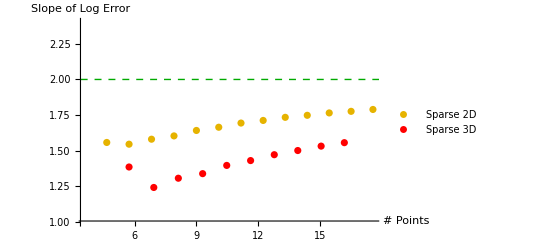

```mathematica
Show[ListPlot[{Table[{Log2[sparseLengths2D[[n]]],-(Log2[sparse2DError⟦n⟧]-Log2[sparse2DError⟦n-1⟧])/(Log2[sparseLengths2D[[n]]]-Log2[sparseLengths2D[[n-1]]])},{n,2,15}],Table[{Log2[sparseLengths3D[[n]]],-(Log2[sparse3DError⟦n⟧]-Log2[sparse3DError⟦n-1⟧])/(Log2[sparseLengths3D[[n]]]-Log2[sparseLengths3D[[n-1]]])},{n,2,12}]},PlotRange->{1,2.4},PlotStyle->{RGBColor[.9,.7,0],Red},PlotLegends->{"Sparse 2D","Sparse 3D"},AxesLabel->{"# Points","Slope of Log Error"}],Graphics[{Dashed,Darker[Green],Line[{{0,2},{18,2}}]}]]
```

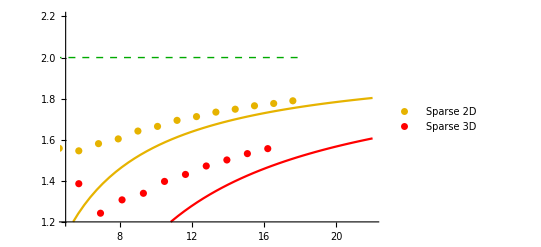

```mathematica
Show[Plot[{-(p^3 ((3 Log[p]^2)/p^3-(2 Log[p]^3)/p^3))/Log[p]^3/.p->2^n,-(p^3 ((6 Log[p]^5)/p^3-(2 Log[p]^6)/p^3))/Log[p]^6/.p->2^n},{n,5,22},PlotStyle->{RGBColor[.9,.7,0],Red},PlotRange->{1.2,2.2}],ListPlot[{Table[{Log2[sparseLengths2D[[n]]],-(Log2[sparse2DError⟦n⟧]-Log2[sparse2DError⟦n-1⟧])/(Log2[sparseLengths2D[[n]]]-Log2[sparseLengths2D[[n-1]]])},{n,2,15}],Table[{Log2[sparseLengths3D[[n]]],-(Log2[sparse3DError⟦n⟧]-Log2[sparse3DError⟦n-1⟧])/(Log2[sparseLengths3D[[n]]]-Log2[sparseLengths3D[[n-1]]])},{n,2,12}]},PlotRange->{1,2.4},PlotStyle->{RGBColor[.9,.7,0],Red},PlotLegends->{"Sparse 2D","Sparse 3D"},AxesLabel->{"# Points","Slope of Log Error"}],Graphics[{Dashed,Darker[Green],Line[{{0,2},{18,2}}]}]]
```

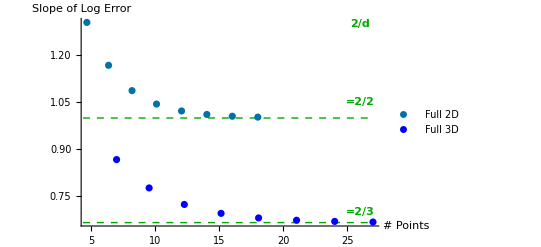

```mathematica
Show[ListPlot[{Table[{Log2[hierLengths2D[[n]]],-(Log2[full2DError⟦n⟧]-Log2[full2DError⟦n-1⟧])/(Log2[hierLengths2D[[n]]]-Log2[hierLengths2D[[n-1]]])},{n,2,9}],Table[{Log2[hierLengths3D[[n]]],-(Log2[full3DError⟦n⟧]-Log2[full3DError⟦n-1⟧])/(Log2[hierLengths3D[[n]]]-Log2[hierLengths3D[[n-1]]])},{n,2,9}]},PlotStyle->{RGBColor[0,.45,.65],Blue},PlotLegends->{"Full 2D","Full 3D"},AxesLabel->{"# Points","Slope of Log Error"}],Graphics[{Dashed,Darker[Green],Line[{{0,1},{27,1}}],Line[{{0,2/3},{27,2/3}}],Text[Style["=2/2",Bold],{26,1.05}],Text[Style["=2/3",Bold],{26,.7}],Text[Style["2/d",Bold],{26,1.3}]}]]
```